## Feynman Diagram

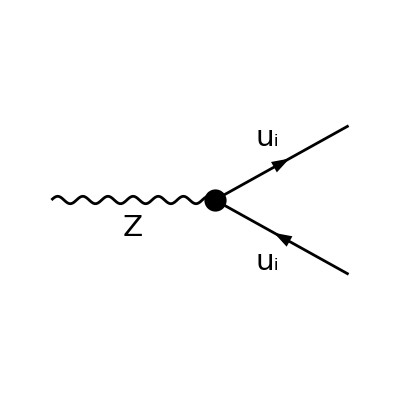

```mathematica
ZtoQQbar=InsertFields[CreateTopologies[0,1->2],{V[2]}->{F[3,{i}],-F[3,{i}]},InsertionLevel->{Classes},Model->"SMQCD"];

Paint[ZtoQQbar,ColumnsXRows->{2,1},Numbering->None,SheetHeader->None,ImageSize->{512,256}];
```

## Amplitude Squared

```mathematica
(|M|)^2=1/3(Subscript[g, 2]/(2cos Subscript[θ, w]))^2 Subscript[ϵ, μ](Subscript[p, 1])SuperStar[Subscript[ϵ, ν]](Subscript[p, 1])Tr [ γ^μ (Subscript[g, V]^(q-Z)-Subscript[g, A]^(q-Z) γ^5)(Subscript[p, 2slash]+Subscript[m, q])γ^ν (Subscript[g, V]^(q-Z)-Subscript[g, A]^(q-Z) γ^5)(Subscript[p, 3slash]-Subscript[m, q̄])]
```

## Trace Calculation

```mathematica
Tr[GA[μ].(Subscript[g, V]-Subscript[g, A] GA5).(GS[p2]+m2).GA[ν].(Subscript[g, V]-Subscript[g, A] GA5).(GS[p3]-m3)];
ChangeDimension[%,D]
%//StandardForm;
```

4 (m2 m3 g_A^2 g^μν+g_A^2 p2^ν p3^μ+g_A^2 p2^μ p3^ν-g_A^2 g^μν (p2·p3)+2 ⅈ g_A g_V ϵ^μνp2p3-m2 m3 g_V^2 g^μν+g_V^2 p2^ν p3^μ+g_V^2 p2^μ p3^ν-g_V^2 g^μν (p2·p3))

Getting rid of imaginary/tensor term ⅈ ϵ^μνσρ

```mathematica
4 (m2 m3 Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Subscript[g, A]^2+Pair[LorentzIndex[μ,D],Momentum[p3,D]] Pair[LorentzIndex[ν,D],Momentum[p2,D]] Subscript[g, A]^2+Pair[LorentzIndex[μ,D],Momentum[p2,D]] Pair[LorentzIndex[ν,D],Momentum[p3,D]] Subscript[g, A]^2-Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Pair[Momentum[p2,D],Momentum[p3,D]] Subscript[g, A]^2-m2 m3 Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Subscript[g, V]^2+Pair[LorentzIndex[μ,D],Momentum[p3,D]] Pair[LorentzIndex[ν,D],Momentum[p2,D]] Subscript[g, V]^2+Pair[LorentzIndex[μ,D],Momentum[p2,D]] Pair[LorentzIndex[ν,D],Momentum[p3,D]] Subscript[g, V]^2-Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Pair[Momentum[p2,D],Momentum[p3,D]] Subscript[g, V]^2)
```

4 (m2 m3 g_A^2 g^μν+g_A^2 p2^ν p3^μ+g_A^2 p2^μ p3^ν-g_A^2 g^μν (p2·p3)-m2 m3 g_V^2 g^μν+g_V^2 p2^ν p3^μ+g_V^2 p2^μ p3^ν-g_V^2 g^μν (p2·p3))

```mathematica
%//Simplify
```

4 (g^μν (g_A^2 (m2 m3-p2·p3)-g_V^2 (m2 m3+p2·p3))+(g_A^2+g_V^2) (p2^ν p3^μ+p2^μ p3^ν))

Expanding and simplifying g^μν (g_A^2 (m2 m3-p2.p3)-g_V^2 (m2 m3+p2.p3)) 
and recombining with previous calculation

```mathematica
Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] ((m2 m3-Pair[Momentum[p2,D],Momentum[p3,D]]) Subscript[g, A]^2-(m2 m3+Pair[Momentum[p2,D],Momentum[p3,D]]) Subscript[g, V]^2)//Expand
```

m2 m3 g_A^2 g^μν-g_A^2 g^μν (p2·p3)-m2 m3 g_V^2 g^μν-g_V^2 g^μν (p2·p3)

```mathematica
TraceCalc==4HoldForm[(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[p, 2]^μ Subscript[p, 3]^ν+Subscript[p, 2]^ν Subscript[p, 3]^μ-g^μν(Subscript[p, 2].Subscript[p, 3]))+(Subscript[g, A]^2-Subscript[g, V]^2)g^μν Subscript[m, 2] Subscript[m, 3]]
```

TraceCalc==4 ((g_A^2+g_V^2) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)+(g_A^2-g_V^2) g^μν m_2 m_3)

m_2=m_3=m_q

```mathematica
TraceCalc==4HoldForm[(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[p, 2]^μ Subscript[p, 3]^ν+Subscript[p, 2]^ν Subscript[p, 3]^μ-g^μν(Subscript[p, 2].Subscript[p, 3]))+(Subscript[g, A]^2-Subscript[g, V]^2)g^μν Subscript[m, q]^2]
TraceCalc==4HoldForm[(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[p, 2]^μ Subscript[p, 3]^ν+Subscript[p, 2]^ν Subscript[p, 3]^μ-g^μν(Subscript[p, 2].Subscript[p, 3]))-(Subscript[g, V]^2-Subscript[g, A]^2)g^μν Subscript[m, q]^2]
```

TraceCalc==4 ((g_A^2+g_V^2) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)+(g_A^2-g_V^2) g^μν m_q^2)

TraceCalc==4 ((g_A^2+g_V^2) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)-(g_V^2-g_A^2) g^μν m_q^2)

## Multiply by Full Propagator

ϵ_μ(p_1)ϵ_ν(p_1)=((p_(1μ)p_(1ν))/M_z^2-g_μν)

A = (g_A^2+g_V^2)

((p_(1μ)p_(1ν))/M_z^2-g_μν) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)

```mathematica
((FV[p1,μ].FV[p1,ν])/Subscript[M, z]^2-MT[μ,ν])*A*(FV[p2,μ].FV[p3,ν]+FV[p2,ν].FV[p3,μ]-MT[μ,ν].SP[p2,p3])//Expand//Contract;
ChangeDimension[%,D]
%/.{Pair[Momentum[p1,D],Momentum[p1,D]]->Subscript[M, z]^2}
```

(2 A (p1·p2) (p1·p3))/M_z^2-(A p1^2 (p2·p3))/M_z^2+2 A (p2·p3)

(2 A (p1·p2) (p1·p3))/M_z^2+A (p2·p3)

(2 A (p1 · p2) (p1·p3))/M_z^2+A (p2·p3),       ( Equation 1 )

B =(g_V^2-g_A^2)

((p_(1μ)p_(1ν))/M_z^2-g_μν) (g^μν m_q^2)

```mathematica
((FV[p1,μ].FV[p1,ν])/Subscript[M, z]^2-MT[μ,ν])*B*(MT[μ,ν].Subscript[m, q]^2)//Expand//Contract;
ChangeDimension[%,D]
%/.{Pair[Momentum[p1,D],Momentum[p1,D]]->Subscript[M, z]^2}
```

(B p1^2 m_q^2)/M_z^2-4 B m_q^2

-3 B m_q^2

-3 B m_q^2,  ( Equation 2 )

Kinematics:   p_1=( M_z ,0 ),  p_2=( M_z/2,p⃗ ),  p_3=( M_z/2,-p⃗ )

```mathematica
one={Subscript[M, z],0};
two={Subscript[M, z]/2,p};
three={Subscript[M, z]/2,p};
one.two
one.three
two.three
```

M_z^2/2

M_z^2/2

M_z^2/4+p^2

Putting Equation 1 and Equation 2 back into TraceCalc:

```mathematica
4(A(2((Subscript[p, 1].Subscript[p, 2]).(Subscript[p, 1].Subscript[p, 3]))/Subscript[M, Z]^2+(Subscript[p, 2].Subscript[p, 3]))-B.(-3 Subscript[m, q]^2))==4((Subscript[g, A]^2+Subscript[g, V]^2)(2((one.two)(one.three))/Subscript[M, z]^2+(two.three))-(Subscript[g, V]^2-Subscript[g, A]^2).(-3 Subscript[m, q]^2))
```

4 (A ((2 p_1.p_2.p_1.p_3)/M_Z^2+p_2.p_3)-B.(-3 m_q^2))==4 ((g_A^2+g_V^2) ((3 M_z^2)/4+p^2)-(g_V^2-g_A^2).(-3 m_q^2))

```mathematica
%/.{p^2-> Subscript[M, z]^2/4-Subscript[m, q]^2}
```

4 (A ((2 p_1.p_2.p_1.p_3)/M_Z^2+p_2.p_3)-B.(-3 m_q^2))==4 ((g_A^2+g_V^2) (M_z^2-m_q^2)-(g_V^2-g_A^2).(-3 m_q^2))

```mathematica
(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[M, z]^2-Subscript[m, q]^2)-(Subscript[g, V]^2-Subscript[g, A]^2)(-3 Subscript[m, q]^2)//Expand
```

-4 g_A^2 m_q^2+g_A^2 M_z^2+2 g_V^2 m_q^2+g_V^2 M_z^2

```mathematica
Collect[%,Subscript[M, z]^2]
```

-4 g_A^2 m_q^2+M_z^2 (g_A^2+g_V^2)+2 g_V^2 m_q^2

```mathematica
Collect[%,Subscript[m, q]^2]
```

m_q^2 (2 g_V^2-4 g_A^2)+M_z^2 (g_A^2+g_V^2)

```mathematica
4((Subscript[g, A]^2+Subscript[g, V]^2).Subscript[M, z]^2+2 Subscript[m, q]^2(Subscript[g, V]^2-2 Subscript[g, A]^2))==4 Subscript[M, z]^2 HoldForm[((Subscript[g, A]^2+Subscript[g, V]^2)+2 Subscript[m, q]^2/Subscript[M, z]^2(Subscript[g, V]^2-2 Subscript[g, A]^2))]
4 Subscript[M, z]^2 HoldForm[((Subscript[g, A]^2+Subscript[g, V]^2)+2(Subscript[m, q]^2/Subscript[M, z]^2).(Subscript[g, V]^2-2 Subscript[g, A]^2))]==4 Subscript[M, z]^2 HoldForm[(Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2+2(Subscript[m, q]^2/Subscript[M, z]^2).((Subscript[g, V]^(q-z))^2-2(Subscript[g, A]^(q-z))^2)]
```

4 (2 m_q^2 (g_V^2-2 g_A^2)+(g_A^2+g_V^2).M_z^2)==4 M_z^2 ((g_A^2+g_V^2)+(2 m_q^2 (g_V^2-2 g_A^2))/M_z^2)

4 M_z^2 ((g_A^2+g_V^2)+2 m_q^2/M_z^2.(g_V^2-2 g_A^2))==4 M_z^2 ((g_A^(q-z))^2+(g_V^(q-z))^2+2 m_q^2/M_z^2.((g_V^(q-z))^2-2 (g_A^(q-z))^2))

```mathematica
(|M|)^2=1/3(Subscript[g, 2]/(2cos Subscript[θ, w]))^2 4 Subscript[M, z]^2 ((Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2+2 (Subscript[m, q]^2/Subscript[M, z]^2).((Subscript[g, V]^(q-z))^2-2 (Subscript[g, A]^(q-z))^2))

(|M|)^2=1/3 Subscript[g, 2]^2/(cos^2 θ) Subscript[M, z]^2 ((Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2+2 (Subscript[m, q]^2/Subscript[M, z]^2).((Subscript[g, V]^(q-z))^2-2 (Subscript[g, A]^(q-z))^2))
```

## Decay (Initial → Final (2 Body))

Γ = (|p⃗|)/(8π M_z^2)(|M|)^2

|p⃗| = √((E)^2-m_2 m_3) = √((M_Z/2)^2-m_2 m_3) = M_Z/2 √(1-4(m_2 m_3)/M_Z^2)

m_2=m_3=m_q

Γ (Z→q q̄) = g_2^2/(24π cos^2 θ M_z^2)M_Z/2 √(1-4 m_q^2/M_Z^2)M_z^2.((g_V^f)^2+(g_A^f)^2+(2 m_q^2 ((g_V^f)^2- 2 (g_A^f)^2))/M_z^2)

∴  Γ (Z→q q̄) =  (g_2^2 M_Z)/(48π cos^2 θ)(( g_V^(q-Z) )^2+( g_A^(q-Z) )^2+2 m_q^2/M_Z^2 (( g_V^(q-Z) )^2-2 ( g_A^(q-Z) )^2))√(1-4 m_q^2/M_Z^2),  (5.44)

## Multiply by Full Propagator (Flip)

ϵ_μ(p_1)ϵ_ν(p_1)=(g_μν-(p_(1μ)p_(1ν))/M_z^2)

A = (g_A^2+g_V^2)

(g_μν-(p_(1μ)p_(1ν))/M_z^2) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)

```mathematica
(MT[μ,ν]-(FV[p1,μ].FV[p1,ν])/Subscript[M, z]^2)*A*(FV[p2,μ].FV[p3,ν]+FV[p2,ν].FV[p3,μ]-MT[μ,ν].SP[p2,p3])//Expand//Contract;
ChangeDimension[%,D]
%/.{Pair[Momentum[p1,D],Momentum[p1,D]]->Subscript[M, z]^2}
```

-(2 A (p1·p2) (p1·p3))/M_z^2+(A p1^2 (p2·p3))/M_z^2-2 A (p2·p3)

-(2 A (p1·p2) (p1·p3))/M_z^2-A (p2·p3)

-(2 A (p1 · p2) (p1·p3))/M_z^2-A (p2·p3),       ( Equation 1 )

B =(g_V^2-g_A^2)

(g_μν-(p_(1μ)p_(1ν))/M_z^2) (g^μν m_q^2)

```mathematica
(MT[μ,ν]-(FV[p1,μ].FV[p1,ν])/Subscript[M, z]^2)*B*(MT[μ,ν].Subscript[m, q]^2)//Expand//Contract;
ChangeDimension[%,D]
%/.{Pair[Momentum[p1,D],Momentum[p1,D]]->Subscript[M, z]^2}
```

4 B m_q^2-(B p1^2 m_q^2)/M_z^2

3 B m_q^2

3 B m_q^2,  ( Equation 2 )

Kinematics:   p_1=( M_z ,0 ),  p_2=( M_z/2,p⃗ ),  p_3=( M_z/2,-p⃗ )

```mathematica
one={Subscript[M, z],0};
two={Subscript[M, z]/2,p};
three={Subscript[M, z]/2,p};
one.two
one.three
two.three
```

M_z^2/2

M_z^2/2

M_z^2/4+p^2

Putting Equation 1 and Equation 2 back into TraceCalc:

```mathematica
4(A(2((Subscript[p, 1].Subscript[p, 2]).(Subscript[p, 1].Subscript[p, 3]))/Subscript[M, Z]^2+(Subscript[p, 2].Subscript[p, 3]))-B.(3 Subscript[m, q]^2))==4((Subscript[g, A]^2+Subscript[g, V]^2)(-2((one.two)(one.three))/Subscript[M, z]^2-(two.three))-(Subscript[g, V]^2-Subscript[g, A]^2).(3 Subscript[m, q]^2))
```

4 (A ((2 p_1.p_2.p_1.p_3)/M_Z^2+p_2.p_3)-B.(3 m_q^2))==4 ((g_A^2+g_V^2) (-(3 M_z^2)/4-p^2)-(g_V^2-g_A^2).(3 m_q^2))

```mathematica
%/.{p^2-> Subscript[M, z]^2/4-Subscript[m, q]^2}
```

4 (A ((2 p_1.p_2.p_1.p_3)/M_Z^2+p_2.p_3)-B.(3 m_q^2))==4 ((g_A^2+g_V^2) (m_q^2-M_z^2)-(g_V^2-g_A^2).(3 m_q^2))

```mathematica
(Subscript[g, A]^2+Subscript[g, V]^2)(-Subscript[M, z]^2+Subscript[m, q]^2)-(Subscript[g, V]^2-Subscript[g, A]^2)(3 Subscript[m, q]^2)//Expand
```

4 g_A^2 m_q^2-g_A^2 M_z^2-2 g_V^2 m_q^2-g_V^2 M_z^2

```mathematica
Collect[%,Subscript[M, z]^2]
```

4 g_A^2 m_q^2+M_z^2 (-g_A^2-g_V^2)-2 g_V^2 m_q^2

```mathematica
Collect[%,Subscript[m, q]^2]
```

m_q^2 (4 g_A^2-2 g_V^2)+M_z^2 (-g_A^2-g_V^2)

```mathematica
4(-(Subscript[g, A]^2+Subscript[g, V]^2).Subscript[M, z]^2+2 Subscript[m, q]^2(2 Subscript[g, A]^2-Subscript[g, V]^2))==4 Subscript[M, z]^2 HoldForm[(-(Subscript[g, A]^2+Subscript[g, V]^2)+2 Subscript[m, q]^2/Subscript[M, z]^2(2 Subscript[g, A]^2-Subscript[g, V]^2))]
-4 Subscript[M, z]^2 HoldForm[((Subscript[g, A]^2+Subscript[g, V]^2)-2(Subscript[m, q]^2/Subscript[M, z]^2).(2 Subscript[g, A]^2-Subscript[g, V]^2))]==-4 Subscript[M, z]^2 HoldForm[(Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2-2(Subscript[m, q]^2/Subscript[M, z]^2).(2(Subscript[g, A]^(q-z))^2-(Subscript[g, V]^(q-z))^2)]
```

4 (2 m_q^2 (2 g_A^2-g_V^2)-(g_A^2+g_V^2).M_z^2)==4 M_z^2 (-(g_A^2+g_V^2)+(2 m_q^2 (2 g_A^2-g_V^2))/M_z^2)

-4 M_z^2 ((g_A^2+g_V^2)-2 m_q^2/M_z^2.(2 g_A^2-g_V^2))==-4 M_z^2 ((g_A^(q-z))^2+(g_V^(q-z))^2-2 m_q^2/M_z^2.(2 (g_A^(q-z))^2-(g_V^(q-z))^2))

```mathematica
(|M|)^2=-1/3(Subscript[g, 2]/(2cos Subscript[θ, w]))^2 4 Subscript[M, z]^2 ((Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2-2 (Subscript[m, q]^2/Subscript[M, z]^2).(2(Subscript[g, A]^(q-z))^2- (Subscript[g, V]^(q-z))^2))

(|M|)^2=-1/3 Subscript[g, 2]^2/(cos^2 θ) Subscript[M, z]^2 ((Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2+2 (Subscript[m, q]^2/Subscript[M, z]^2).((Subscript[g, V]^(q-z))^2-2 (Subscript[g, A]^(q-z))^2))
```

## Decay (Initial → Final (2 Body)) (Flip Propagator)

Γ = (|p⃗|)/(8π M_z^2)(|M|)^2

|p⃗| = √((E)^2-m_2 m_3) = √((M_Z/2)^2-m_2 m_3) = M_Z/2 √(1-4(m_2 m_3)/M_Z^2)

m_2=m_3=m_q

Γ (Z→q q̄) = -g_2^2/(24π cos^2 θ M_z^2)M_Z/2 √(1-4 m_q^2/M_Z^2)M_z^2.((g_V^f)^2+(g_A^f)^2+(2 m_q^2 ((g_V^f)^2-2 (g_A^f)^2))/M_z^2)

∴  Γ (Z→q q̄) =  -(g_2^2 M_Z)/(48π cos^2 θ)(( g_V^(q-Z) )^2+( g_A^(q-Z) )^2+2 m_q^2/M_Z^2 (( g_V^(q-Z) )^2-2 ( g_A^(q-Z) )^2))√(1-4 m_q^2/M_Z^2),  (5.44)

## Amplitude Squared (m_3>0)

```mathematica
(|M|)^2=1/3(Subscript[g, 2]/(2cos Subscript[θ, w]))^2 Subscript[ϵ, μ](Subscript[p, 1])SuperStar[Subscript[ϵ, ν]](Subscript[p, 1])Tr [ γ^μ (Subscript[g, V]^(q-Z)-Subscript[g, A]^(q-Z) γ^5)(Subscript[p, 2slash]+Subscript[m, q])γ^ν (Subscript[g, V]^(q-Z)-Subscript[g, A]^(q-Z) γ^5)(Subscript[p, 3slash]+Subscript[m, q̄])]
```

## Trace Calculation (m_3>0)

```mathematica
Tr[GA[μ].(Subscript[g, V]-Subscript[g, A] GA5).(GS[p2]+m2).GA[ν].(Subscript[g, V]-Subscript[g, A] GA5).(GS[p3]+m3)];
ChangeDimension[%,D]
%//StandardForm;
```

-4 (m2 m3 g_A^2 g^μν-g_A^2 p2^ν p3^μ-g_A^2 p2^μ p3^ν+g_A^2 g^μν (p2·p3)-2 ⅈ g_A g_V ϵ^μνp2p3-m2 m3 g_V^2 g^μν-g_V^2 p2^ν p3^μ-g_V^2 p2^μ p3^ν+g_V^2 g^μν (p2·p3))

Getting rid of imaginary/tensor term ⅈ ϵ^μνσρ

```mathematica
-4 (m2 m3 Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Subscript[g, A]^2-Pair[LorentzIndex[μ,D],Momentum[p3,D]] Pair[LorentzIndex[ν,D],Momentum[p2,D]] Subscript[g, A]^2-Pair[LorentzIndex[μ,D],Momentum[p2,D]] Pair[LorentzIndex[ν,D],Momentum[p3,D]] Subscript[g, A]^2+Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Pair[Momentum[p2,D],Momentum[p3,D]] Subscript[g, A]^2-m2 m3 Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Subscript[g, V]^2-Pair[LorentzIndex[μ,D],Momentum[p3,D]] Pair[LorentzIndex[ν,D],Momentum[p2,D]] Subscript[g, V]^2-Pair[LorentzIndex[μ,D],Momentum[p2,D]] Pair[LorentzIndex[ν,D],Momentum[p3,D]] Subscript[g, V]^2+Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] Pair[Momentum[p2,D],Momentum[p3,D]] Subscript[g, V]^2)
```

-4 (m2 m3 g_A^2 g^μν-g_A^2 p2^ν p3^μ-g_A^2 p2^μ p3^ν+g_A^2 g^μν (p2·p3)-m2 m3 g_V^2 g^μν-g_V^2 p2^ν p3^μ-g_V^2 p2^μ p3^ν+g_V^2 g^μν (p2·p3))

```mathematica
%//Expand//Simplify
```

4 (g_A^2+g_V^2) (p2^ν p3^μ+p2^μ p3^ν)-4 g^μν (g_A^2 (m2 m3+p2·p3)+g_V^2 (p2·p3-m2 m3))

Expanding and simplifying -4 g^μν (g_A^2 (m2 m3+p2.p3)+g_V^2 (p2.p3-m2 m3)) 
and recombining with previous calculation

```mathematica
-4Pair[LorentzIndex[μ,D],LorentzIndex[ν,D]] ((m2 m3+Pair[Momentum[p2,D],Momentum[p3,D]]) Subscript[g, A]^2+(-m2 m3+Pair[Momentum[p2,D],Momentum[p3,D]]) Subscript[g, V]^2)//Expand
```

-4 m2 m3 g_A^2 g^μν-4 g_A^2 g^μν (p2·p3)+4 m2 m3 g_V^2 g^μν-4 g_V^2 g^μν (p2·p3)

```mathematica
Collect[%,Subscript[g, A]^2]
```

g_A^2 (-4 m2 m3 g^μν-4 g^μν (p2·p3))+4 m2 m3 g_V^2 g^μν-4 g_V^2 g^μν (p2·p3)

```mathematica
Collect[%,Subscript[g, V]^2]
```

g_A^2 (-4 m2 m3 g^μν-4 g^μν (p2·p3))+g_V^2 (4 m2 m3 g^μν-4 g^μν (p2·p3))

```mathematica
TraceCalc==4HoldForm[(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[p, 2]^μ Subscript[p, 3]^ν+Subscript[p, 2]^ν Subscript[p, 3]^μ-g^μν(Subscript[p, 2].Subscript[p, 3]))+(Subscript[g, V]^2-Subscript[g, A]^2)g^μν Subscript[m, 2] Subscript[m, 3]]
```

TraceCalc==4 ((g_A^2+g_V^2) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)+(g_V^2-g_A^2) g^μν m_2 m_3)

m_2=m_3=m_q

```mathematica
TraceCalc==4HoldForm[(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[p, 2]^μ Subscript[p, 3]^ν+Subscript[p, 2]^ν Subscript[p, 3]^μ-g^μν(Subscript[p, 2].Subscript[p, 3]))+(Subscript[g, V]^2-Subscript[g, A]^2)g^μν Subscript[m, q]^2]
TraceCalc==4HoldForm[(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[p, 2]^μ Subscript[p, 3]^ν+Subscript[p, 2]^ν Subscript[p, 3]^μ-g^μν(Subscript[p, 2].Subscript[p, 3]))-(Subscript[g, A]^2-Subscript[g, V]^2)g^μν Subscript[m, q]^2]
```

TraceCalc==4 ((g_A^2+g_V^2) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)+(g_V^2-g_A^2) g^μν m_q^2)

TraceCalc==4 ((g_A^2+g_V^2) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)-(g_A^2-g_V^2) g^μν m_q^2)

## Multiply by Full Propagator (m_3>0)

ϵ_μ(p_1)ϵ_ν(p_1)=((p_(1μ)p_(1ν))/M_z^2-g_μν)

A = (g_A^2+g_V^2)

((p_(1μ)p_(1ν))/M_z^2-g_μν) (p_2^μ p_3^ν+p_2^ν p_3^μ-g^μν p_2.p_3)

```mathematica
((FV[p1,μ].FV[p1,ν])/Subscript[M, z]^2-MT[μ,ν])*A*(FV[p2,μ].FV[p3,ν]+FV[p2,ν].FV[p3,μ]-MT[μ,ν].SP[p2,p3])//Expand//Contract;
ChangeDimension[%,D]
%/.{Pair[Momentum[p1,D],Momentum[p1,D]]->Subscript[M, z]^2}
```

(2 A (p1·p2) (p1·p3))/M_z^2-(A p1^2 (p2·p3))/M_z^2+2 A (p2·p3)

(2 A (p1·p2) (p1·p3))/M_z^2+A (p2·p3)

(2 A (p1 · p2) (p1·p3))/M_z^2+A (p2·p3),       ( Equation 1 )

B =(g_A^2-g_V^2)

((p_(1μ)p_(1ν))/M_z^2-g_μν) (g^μν m_q^2)

```mathematica
((FV[p1,μ].FV[p1,ν])/Subscript[M, z]^2-MT[μ,ν])*B*(MT[μ,ν].Subscript[m, q]^2)//Expand//Contract;
ChangeDimension[%,D]
%/.{Pair[Momentum[p1,D],Momentum[p1,D]]->Subscript[M, z]^2}
```

(B p1^2 m_q^2)/M_z^2-4 B m_q^2

-3 B m_q^2

-3 B m_q^2,  ( Equation 2 )

Kinematics:   p_1=( M_z ,0 ),  p_2=( M_z/2,p⃗ ),  p_3=( M_z/2,-p⃗ )

```mathematica
one={Subscript[M, z],0};
two={Subscript[M, z]/2,p};
three={Subscript[M, z]/2,p};
one.two
one.three
two.three
```

M_z^2/2

M_z^2/2

M_z^2/4+p^2

Putting Equation 1 and Equation 2 back into TraceCalc:

```mathematica
4(A(2((Subscript[p, 1].Subscript[p, 2]).(Subscript[p, 1].Subscript[p, 3]))/Subscript[M, Z]^2+(Subscript[p, 2].Subscript[p, 3]))-B.(-3 Subscript[m, q]^2))==4((Subscript[g, A]^2+Subscript[g, V]^2)(2((one.two)(one.three))/Subscript[M, z]^2+(two.three))-(Subscript[g, A]^2-Subscript[g, V]^2).(-3 Subscript[m, q]^2))
```

4 (A ((2 p_1.p_2.p_1.p_3)/M_Z^2+p_2.p_3)-B.(-3 m_q^2))==4 ((g_A^2+g_V^2) ((3 M_z^2)/4+p^2)-(g_A^2-g_V^2).(-3 m_q^2))

```mathematica
%/.{p^2-> Subscript[M, z]^2/4-Subscript[m, q]^2}
```

4 (A ((2 p_1.p_2.p_1.p_3)/M_Z^2+p_2.p_3)-B.(-3 m_q^2))==4 ((g_A^2+g_V^2) (M_z^2-m_q^2)-(g_A^2-g_V^2).(-3 m_q^2))

```mathematica
(Subscript[g, A]^2+Subscript[g, V]^2)(Subscript[M, z]^2-Subscript[m, q]^2)-(Subscript[g, A]^2-Subscript[g, V]^2)(-3 Subscript[m, q]^2)//Expand
```

2 g_A^2 m_q^2+g_A^2 M_z^2-4 g_V^2 m_q^2+g_V^2 M_z^2

```mathematica
Collect[%,Subscript[M, z]^2]
```

2 g_A^2 m_q^2+M_z^2 (g_A^2+g_V^2)-4 g_V^2 m_q^2

```mathematica
Collect[%,Subscript[m, q]^2]
```

m_q^2 (2 g_A^2-4 g_V^2)+M_z^2 (g_A^2+g_V^2)

```mathematica
4((Subscript[g, A]^2+Subscript[g, V]^2).Subscript[M, z]^2+2 Subscript[m, q]^2(Subscript[g, A]^2-2 Subscript[g, V]^2))==4 Subscript[M, z]^2 HoldForm[((Subscript[g, A]^2+Subscript[g, V]^2)+2 Subscript[m, q]^2/Subscript[M, z]^2(Subscript[g, A]^2-2 Subscript[g, V]^2))]
4 Subscript[M, z]^2 HoldForm[((Subscript[g, A]^2+Subscript[g, V]^2)+2(Subscript[m, q]^2/Subscript[M, z]^2).(Subscript[g, A]^2-2 Subscript[g, V]^2))]==4 Subscript[M, z]^2 HoldForm[(Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2+2(Subscript[m, q]^2/Subscript[M, z]^2).((Subscript[g, A]^(q-z))^2-2(Subscript[g, V]^(q-z))^2)]
```

4 (2 m_q^2 (g_A^2-2 g_V^2)+(g_A^2+g_V^2).M_z^2)==4 M_z^2 ((g_A^2+g_V^2)+(2 m_q^2 (g_A^2-2 g_V^2))/M_z^2)

4 M_z^2 ((g_A^2+g_V^2)+2 m_q^2/M_z^2.(g_A^2-2 g_V^2))==4 M_z^2 ((g_A^(q-z))^2+(g_V^(q-z))^2+2 m_q^2/M_z^2.((g_A^(q-z))^2-2 (g_V^(q-z))^2))

```mathematica
(|M|)^2=1/3(Subscript[g, 2]/(2cos Subscript[θ, w]))^2 4 Subscript[M, z]^2 ((Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2+2 (Subscript[m, q]^2/Subscript[M, z]^2).((Subscript[g, A]^(q-z))^2-2 (Subscript[g, V]^(q-z))^2))

(|M|)^2=1/3 Subscript[g, 2]^2/(cos^2 θ) Subscript[M, z]^2 ((Subscript[g, A]^(q-z))^2+(Subscript[g, V]^(q-z))^2+2 (Subscript[m, q]^2/Subscript[M, z]^2).((Subscript[g, A]^(q-z))^2-2 (Subscript[g, V]^(q-z))^2))
```

## Decay (Initial → Final (2 Body)) (m_3>0)

Γ = (|p⃗|)/(8π M_z^2)(|M|)^2

|p⃗| = √((E)^2-m_2 m_3) = √((M_Z/2)^2-m_2 m_3) = M_Z/2 √(1-4(m_2 m_3)/M_Z^2)

m_2=m_3=m_q

Γ (Z→q q̄) = g_2^2/(24π cos^2 θ M_z^2)M_Z/2 √(1-4 m_q^2/M_Z^2)M_z^2.((g_V^f)^2+(g_A^f)^2+(2 m_q^2 ((g_A^f)^2- 2 (g_V^f)^2))/M_z^2)

∴  Γ (Z→q q̄) =  (g_2^2 M_Z)/(48π cos^2 θ)(( g_A^(q-Z) )^2+( g_V^(q-Z) )^2+2 m_q^2/M_Z^2 (( g_A^(q-Z) )^2-2 ( g_V^(q-Z) )^2))√(1-4 m_q^2/M_Z^2),  (5.44)

```mathematica
(|M|)^2= 4 e^4 ((Eg^2+p^2 cos^2(θ))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2))

(|M|)^2= 4 e^4 ((Eg^2+p^2 cos^2(θ))/(m^2+p^2 sin^2(θ))+(2 m^2)/(m^2+p^2 sin^2(θ))-(2 m^4)/((m^2+p^2 sin^2(θ))^2))
```